First, build a Jacobian matrix based on the N-resource, 1 mid-consumer, and 1 top-consumer system.

```mathematica
(* Number of prey *)
Num = 2;
(* Define the Jacobian Matrix dimensions *) 
JM = Table[0,{i,Num+2},{j,Num+2}];
(* Fill in the resource elements of the matrix *)
Rii = Subscript[a,x]*(Subscript[s,x]-Subscript[b,x]*Subscript[m,x]-Subscript[bb,x]*Subscript[f,{x,x}]);
Rijtop = -Subscript[a,x]*Subscript[b,x]*Subscript[f,{x,y}];
Rijside = -Subscript[a,y]*Subscript[b,y]*Subscript[f,{y,x}];
Table[
If[i==j,JM[[i,j]]=Rii/.{x->i},
If[i<j,
JM[[i,j]] = Rijtop/.{x->i,y->j},
JM[[i,j]] = Rijside/.{x->j,y->i}
]
],{i,1,Num},{j,1,Num}];
(*Very complicated effort to fill in the consumer and top predator elements*)
ConsVecside = Join[Table[Subscript[a,c]*Subscript[g,i],{i,Num}],{Subscript[a,c]*(Subscript[g,c]-Subscript[b,c]*Subscript[m,c]-Subscript[bb,c]*Subscript[h,c]),-Subscript[a,c]*Subscript[bb,c]*Subscript[h,p]}];
PredVecside = Join[Table[0,{i,Num}],{Subscript[a,p]*Subscript[h,c],Subscript[a,p]*(Subscript[h,p]-Subscript[m,p])}];
ConsVectop = Join[Table[-Subscript[a,i]*Subscript[bb,i]*Subscript[f,{i,c}],{i,Num}],{ConsVecside[[Num+1]],PredVecside[[Num+1]]}];
PredVectop = Join[Table[0,{Num}],{ConsVecside[[Num+2]],PredVecside[[Num+2]]}];
Table[JM[[Num+1,i]] =ConsVecside[[i]],{i,Num+2}];
Table[JM[[Num+2,i]] =PredVecside[[i]],{i,Num+2}];
Table[JM[[i,Num+1]] =ConsVectop[[i]],{i,Num+2}];
Table[JM[[i,Num+2]] =PredVectop[[i]],{i,Num+2}];
JM//MatrixForm
```

(a_1 (-bb_1 f_{1,1}-b_1 m_1+s_1) | -a_1 b_1 f_{1,2} | -a_1 bb_1 f_{1,c} | 0
-a_2 b_2 f_{2,1} | a_2 (-bb_2 f_{2,2}-b_2 m_2+s_2) | -a_2 bb_2 f_{2,c} | 0
a_c g_1 | a_c g_2 | a_c (g_c-bb_c h_c-b_c m_c) | -a_c bb_c h_p
0 | 0 | a_p h_c | a_p (h_p-m_p))

Now we will substitute in the relationships of elasticities to the total amount of prey available to the mid-consumer species.

```mathematica
JMM = Table[0,{i,Num+2},{j,Num+2}];
Table[
If[i==j,
(*On-Diagonal*)
JMM[[i,j]]=JM[[i,j]]/.{
Subscript[f,{i,j}]->Subscript[χ,i]*Subscript[λ,i]*(Subscript[λ,t]+Subscript[g,t]-1),
Subscript[f,{i,c}]->Subscript[g,c],
Subscript[g,i]->Subscript[χ,i]*Subscript[λ,i]*Subscript[g,t],
Subscript[bb,i]->(1-Subscript[b,i]),
Subscript[bb,c]->(1-Subscript[b,c]),
Subscript[bb,p]->(1-Subscript[b,p])
},
(*Off-Diagonal*)
JMM[[i,j]] = JM[[i,j]]/.{
Subscript[f,{i,j}]->Subscript[χ,j]*Subscript[λ,j],
Subscript[f,{j,i}]->Subscript[χ,i]*Subscript[λ,i],
Subscript[f,{i,c}]->Subscript[g,c],
Subscript[g,i]->Subscript[χ,i]*Subscript[λ,i]*Subscript[g,t],
Subscript[g,j]->Subscript[χ,j]*Subscript[λ,j]*Subscript[g,t],
Subscript[bb,i]->(1-Subscript[b,i]),
Subscript[bb,j]->(1-Subscript[b,j]),
Subscript[bb,c]->(1-Subscript[b,c]),
Subscript[bb,p]->(1-Subscript[b,p])
}
],{i,Num+2},{j,Num+2}];
JMM//MatrixForm
```

(a_1 (-b_1 m_1+s_1-(1-b_1) λ_1 (-1+g_t+λ_t) χ_1) | -a_1 b_1 λ_2 χ_2 | -a_1 (1-b_1) g_c | 0
-a_2 b_2 λ_1 χ_1 | a_2 (-b_2 m_2+s_2-(1-b_2) λ_2 (-1+g_t+λ_t) χ_2) | -a_2 (1-b_2) g_c | 0
a_c g_t λ_1 χ_1 | a_c g_t λ_2 χ_2 | a_c (g_c-(1-b_c) h_c-b_c m_c) | -a_c (1-b_c) h_p
0 | 0 | a_p h_c | a_p (h_p-m_p))

```mathematica
PreyContribution = {0.25,0.25,0.25,0.25};
PJMM = JMM/.Join[
Flatten[
Table[
{
Subscript[s,i]->1,
Subscript[m,i]->1,
Subscript[b,i]->0.3,
Subscript[a,i]->1,
Subscript[λ,i]->2,
Subscript[χ,i]->PreyContribution[[i]]
},
{i,1,Num}]
],
{
Subscript[a,c]->0.5,
Subscript[a,p]->0.25,
Subscript[b,c]->0.3,
Subscript[m,c]->1,
Subscript[m,p]->1,
Subscript[h,c]->0.5,
Subscript[h,p]->0.5
}];
PJMM//MatrixForm
```

(0.7-0.35 (-1+g_t+λ_t) | -0.15 | -0.7 g_c | 0
-0.15 | 0.7-0.35 (-1+g_t+λ_t) | -0.7 g_c | 0
0.25 g_t | 0.25 g_t | 0.5 (-0.65+g_c) | -0.175
0 | 0 | 0.125 | -0.125)

```mathematica
Manipulate[
FullPJMM=PJMM/.{Subscript[g,t]->GT,Subscript[λ,t]->LT,Subscript[g,c]->GC};
EValues = Eigenvalues[N[FullPJMM]];
MEV = Max[Re[EValues]];
{
ArrayPlot[FullPJMM,PlotTheme->"Detailed",ColorFunction->"RedBlueTones",PlotRange->{-5,5},PlotLegends->Placed[Automatic,Below]],
ListPlot[Transpose[{Re[EValues],Im[EValues]}],Frame->True,PlotRange->{{-3,3},{-3,3}},AspectRatio->1,PlotStyle->PointSize[Large],FrameLabel->{"Re","Im",MEV}]
},
{GT,0,3},{LT,0,3},{GC,0,3}]
```

ArrayPlot::mat: Argument PJMM at position 1 is not a list of lists.

Transpose::nmtx: The first two levels of {Re[Eigenvalues[PJMM]], Im[Eigenvalues[PJMM]]} cannot be transposed.

ListPlot::lpn: Transpose[{Re[Eigenvalues[PJMM]], Im[Eigenvalues[PJMM]]}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ArrayPlot::mat: Argument PJMM at position 1 is not a list of lists.

Across dietary evenness

```mathematica
Evenness = Table[i,{i,0,1,0.1}];
LI = Table[i,{i,0,2,0.2}];
Leven = Length[Evenness];
LLI = Length[LI];
PSW = Table[0,{Leven},{LLI}];
Table[
w=Evenness[[e]];
v1 = w* {0.25,0.25,0.25,0.25};
v2 = (1-w)*{0,0,0,1};
PreyContribution =v1+v2;
PJMM = JMM/.Join[
Flatten[
Table[
{
Subscript[s,i]->1,
Subscript[m,i]->1,
Subscript[b,i]->0.3,
Subscript[a,i]->1,
Subscript[λ,i]->LI[[l]],
Subscript[χ,i]->PreyContribution[[i]]
},
{i,1,Num}]
],
{
Subscript[a,c]->0.5,
Subscript[a,p]->0.25,
Subscript[b,c]->0.3,
Subscript[m,c]->1,
Subscript[m,p]->1,
Subscript[h,c]->0.5,
Subscript[h,p]->0.6
}];
SW = Table[0,{29791}];
tic=0;
Table[
tic=tic+1;
FullPJMM=PJMM/.{Subscript[g,t]->x,Subscript[λ,t]->y,Subscript[g,c]->z};
EValues = Eigenvalues[N[FullPJMM]];
MEV = Max[Re[EValues]];
If[MEV<0,
SW[[tic]]=1,
SW[[tic]]=0
],{x,0,3,0.1},{y,0,3,0.1},{z,0,3,0.1}];
PSW[[e,l] ]= N[Total[Flatten[SW]]/29791],
{e,1,Leven},{l,1,LLI}];
(*ListPlot[Transpose[{Evenness,PSW}]]*)
```

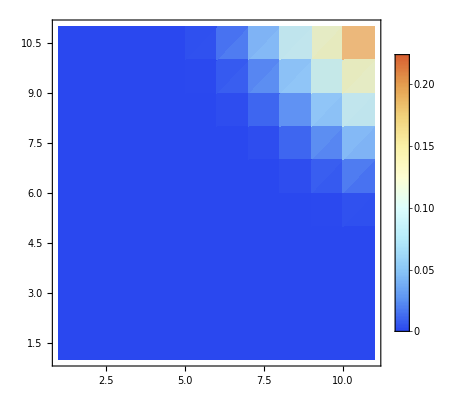

```mathematica
ListDensityPlot[PSW,ColorFunction->"LightTemperatureMap",PlotRange->All,PlotTheme->"Detailed"]
```

```mathematica
LI
```

{0.,0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8,2.}

```mathematica
PreyContribution
```

{0.25,0.25,0.25,0.25}